### Inizializzo tutti i parametri

```mathematica
p[0,x_]=1.;       
q[x_]=Sin[1-x]/(1.-Cos[1]);
w[0]=NIntegrate[x p[0,x],{x,0,1}];
β=0.1;    α=2.;     
γ[β_]:=1-β NIntegrate[q[x]/(1-x),{x,0,1}];
```

### Procedo con l' evoluzione e plotto alcune delle distribuzioni ottenute, assieme alla distribuzione limite (q(dx))/(1-x) (privata della distribuzione δ)

```mathematica
iter=500;
Do[
     p[n,x_Real]=(1-β)/w[n-1] x p[n-1,x] +β q[x] ;  
     w[n]=NIntegrate[x p[n,x],{x,0,1}],
     {n,1,iter}]//AbsoluteTiming
```

{959.332,Null}

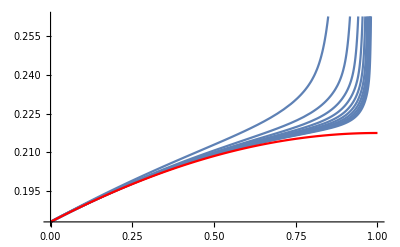

```mathematica
Show[    
	Plot[Table[p[50n,x],{n,1,iter/50}],{x,0,1}],
	Plot[β q[x]/(1-x),{x,0,1},PlotStyle->Red]]
```

### Avvio la verifica del teorema 1.7 per x=10 e x=30

```mathematica
x1=10;       x2=30;
LimiteTeorico1=γ[β]/Gamma[α] NIntegrate[y^(α-1)E^-y,{y,0,x1}];
LimiteTeorico2=γ[β]/Gamma[α] NIntegrate[y^(α-1)E^-y,{y,0,x2}];
data1=Table[NIntegrate[p[n,v],{v,1-x1/n,1}],{n,1,500,10}];
data2=Table[NIntegrate[p[n,v],{v,1-x1/n,1}],{n,1,500,10}];
```

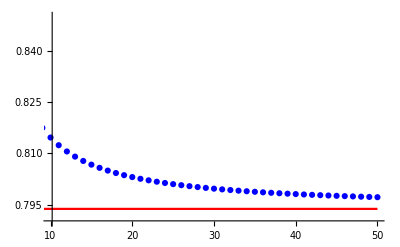

```mathematica
Show[ListPlot[data1,PlotStyle->Blue,PlotRange->{{10,50},{0.79,0.85}}],  
	Plot[0j +LimiteTeorico1,{j,1,Length[data1]},PlotStyle->Red]]
```

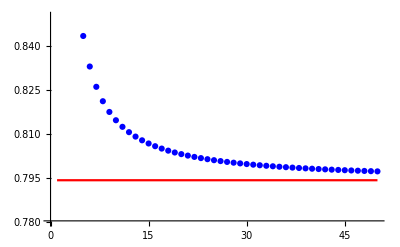

```mathematica
Show[ListPlot[data2,PlotStyle->Blue,PlotRange->{0.78,0.85}],  
	Plot[0j +LimiteTeorico2,{j,1,Length[data2]},PlotStyle->Red]]
```